```mathematica
Quiet[<<PhysicalApplications`Astrophysics`GravitationalWaves`InspiralWaves`;
<<PhysicalApplications`Astrophysics`GravitationalWaves`Detectors`Detector`;
<<PhysicalApplications`Astrophysics`GravitationalWaves`Detectors`Miscellaneous`;
<<PhysicalApplications`Astrophysics`Cosmology`Kinematics`;]
```

--------Retrieving LALInspiralWaveforms.m --------

++ Implement: Injection waveforms: STPN waveforms!

++ Bugs: InspiralTemplate: no orientation? (can't change polarization angle?)
                 hcross implemented manually (complex); check relative factors via inclination.
		 	[assumes HARDCODED NONSPINNING l=|m|=2 amplitude factors]
                 FrequencyComplex  broken (still 1-sided), TimeComplex may pick wrong phase

++ Bugs: TaylorF2 waveform not reconstructed (fourier?)

++ Bugs: alternate sampling rate causes crash.  Currently picks default 2048 Hz

--------Retrieving LALInspiralWaveformsFourierStrainAmplitude.m --------

++ WARNING: PN order convention needs updates!

++ To do:
    - fix: does not evolve when |L|<|S| !  
      Need to insure time refinement then  
    - option to DISABLE r evolution (faster DE solutions for long orbits):
       Add DEMO
    - alternate orders, omega(r) forms.  Options to select different orders (no spin/spin; no quad-monopole)
    - SANE END POINT: evolve to final condition
    - PRECESSION PHASE: track it as well...
    - sanity tests (default; interface with NDSolve tools?: prebuilt BinaryPNS) -> check accuracy/stability
    -
    - apply arbitrary rotations to initial data (default positions, orientations)
    - WAVEFORM EXTRACTION: 0th order, + higher harmonics 
    - hamiltonians?  Use HamiltonanODE tools/symplectic integrators
    - rangewrap output, for safety/use
    - document using L as Lnewtonian
    - poincare sections (via EventLocator) : just in 'demo'?

Debugme: SPA phase expression: confirm agreement (log terms esp)

+++ Aligned spin: Fix amplitude scaling correctly...

++ BUGS: Need to update LAL extractor to sensibly update cutoff frequencies, valid range

--------Retrieving LALMetaio.m --------

--------Retrieving LALInspiralOverlaps.m --------

++LALInspiralWaveformOverlap: 
  Warnings:  Waveforms
     -TaylorF2 broken?! Should not be -- works with raw InspiralOverlap
     -EOBNR crashes link 
  Warnings: Implementation
    - Overlap crashes if parameter seperation too far (memory leak in duration?)

--------Retrieving LALInspiralWaveformsBankEfficiency.m --------

WARNING: This code uses command-line scripts, which generally require properly set environment variables.

WARNING: This code probably only works reliably for l=|m|=2 waveforms (i.e., no inclination effects, spin, multiple harmonics, etc)

--------Retrieving metadataBayesianPostProcessing.m --------

URGENT: Update metadata file to use lookupBindings

WARNING: Recode BayesianPosteriorSamples carefully to use clean dependencies, not duplicated code

++ WARNING: PN order convention needs updates!

++ To do:
    - fix: does not evolve when |L|<|S| !  
      Need to insure time refinement then  
    - option to DISABLE r evolution (faster DE solutions for long orbits):
       Add DEMO
    - alternate orders, omega(r) forms.  Options to select different orders (no spin/spin; no quad-monopole)
    - SANE END POINT: evolve to final condition
    - PRECESSION PHASE: track it as well...
    - sanity tests (default; interface with NDSolve tools?: prebuilt BinaryPNS) -> check accuracy/stability
    -
    - apply arbitrary rotations to initial data (default positions, orientations)
    - WAVEFORM EXTRACTION: 0th order, + higher harmonics 
    - hamiltonians?  Use HamiltonanODE tools/symplectic integrators
    - rangewrap output, for safety/use
    - document using L as Lnewtonian
    - poincare sections (via EventLocator) : just in 'demo'?

Debugme: SPA phase expression: confirm agreement (log terms esp)

+++ Aligned spin: Fix amplitude scaling correctly...

dOperator development: Ok.

DOperator development: Ok.

+++ WARNING: Fisher matrix never debugged to work for log terms.  Does not correctly identify 'J' terms for things without 'f' coefficients though implemented.  Very  important to do the numerical evaluation correctly

+++ WARNING: Take care with evaluating the 'J' expressions...these do not (??) INCLUDE F POWERS? (I thought they did...). debug, make sure amplitude fators included

dOperator development: Ok.

DOperator development: Ok.

Cosmology:Kinematics: Warnings : Assumptions inherent in code only apply at relatively low redshifts z<10^9, so T<<m_e

```mathematica
ΩM=0.3;
ΩΛ=0.7;
c=3*10^8;
G=6.674*10^-11;
M0=(1.989*10^30 *G)/c^2;
λ=(3*10^-6)/(1.989*10^30);
H0=70/(3.08567758*10^19);

constant=(√((7.481503782142397*10^43)^-1));
constant=(8 λ(π G)^(5/3))/(9 H0^3 c^2)
```

9.44226×10^-17

```mathematica
constant = constant*(NIntegrate[1/Mc^2,{Mc,10 M0,50 M0}])^-1
```

1.74086×10^-12

```mathematica
strainAt//Clear;
strainAt[MInMsun_,z_?NumberQ,f_?NumberQ] := gwFourierStrainModelFunctionPlanarSymmetry["Phenomenological","IMRPhenomB"][f, (1+z)MInMsun/2,(1+z) MInMsun/2,0,0] (1 Mega Parsec)/PracticalDistanceLuminosity[z];

En//Clear;
En[z_]:=√(ΩM(1+z)^3+ΩΛ);

Pok//Clear;
Pok[z_,Mc_,Dres_]:=If[PracticalDistanceLuminosity[z]/(Dres(Mc/(1.2 M0))^(5/6) Mega Parsec)<1,DetectorCumulativeAngleFactorGreater["MonteCarlo"][PracticalDistanceLuminosity[z]/(Dres(Mc/(1.2 M0))^(5/6) Mega Parsec)],0];

Rv//Clear;
Rv[z_]:=0.015 (1+z)^2.7/(1+((1+z)/2.9)^5.6);
```

```mathematica
fref = 10;
zref = 0.01;
```

```mathematica
F//Clear
F[Mc_,f_]:=Mc^(5/3) (f/c)^(2/3)((f/fref)^(7/6)strainAt[Mc 2*2^(1/5)/M0,zref,f]/strainAt[Mc 2*2^(1/5)/M0,zref,fref])^2

PDFm//Clear
PDFm[Mc_]:=1/Mc^2

FPDFm//Clear
FPDFm[f_,Mc_]:=F[Mc,f]PDFm[Mc]

FPDF//Clear
FPDF[f_]:=NIntegrate[FPDFm[f,Mc],{Mc,10 M0,50 M0}]
```

```mathematica
p//Clear;
p[f_,z_,Dres_]:=Quiet[NIntegrate[FPDFm[f,Mc](Rv[z]Pok[z,Mc,Dres])/((1+z)^(1/3)En[z]),{Mc,10 M0,50 M0}]];

p0//Clear;
p0[f_,z_,Dres_]:=Quiet[NIntegrate[FPDFm[f,Mc] Rv[z]/((1+z)^(1/3)En[z]),{Mc,10 M0,50 M0}]];
```

```mathematica
p0table={};


Quiet[Do[f=10^(.1j);
Do[z=i/10-1/10;
p0table=Append[p0table,{f,z,p0[f,z,440]}],{i,61}]
Print[j],{j,53}]]
```

```mathematica
p0interp[f_,z_]:=Interpolation[p0table][f,z]
```

```mathematica
P0[f_]:=Quiet[NIntegrate[p0interp[f,z],{z,0,6}]]
```

```mathematica
p1table={};


Do[f=10^(.1j);
Do[z=i/10-1/10;
p1table=Append[p1table,{f,z,p[f,z,440]}],{i,61}]
Print[j],{j,53}]
```

```mathematica
p1interp[f_,z_]:=Interpolation[p1table][f,z]
```

```mathematica
P1[f_]:=Quiet[NIntegrate[p1interp[f,z],{z,0,6}]]
```

```mathematica
p2table={};


Do[f=10^(.1j);
Do[z=i/10-1/20;
p2table=Append[p2table,{f,z,p[f,z,440*17]}],{i,61}]
Print[j],{j,53}]
```

```mathematica
p2interp[f_,z_]:=Interpolation[p2table][f,z]
```

```mathematica
P2[f_]:=Quiet[NIntegrate[p2interp[f,z],{z,0,6}]]
```

```mathematica
total=Quiet[NIntegrate[constant P0[f],{f,0,10^5.3}]]/M0//N
```

5.93476×10^-15

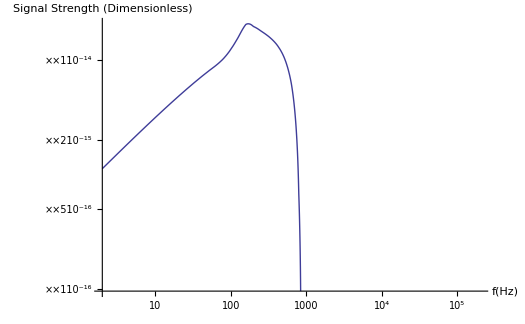

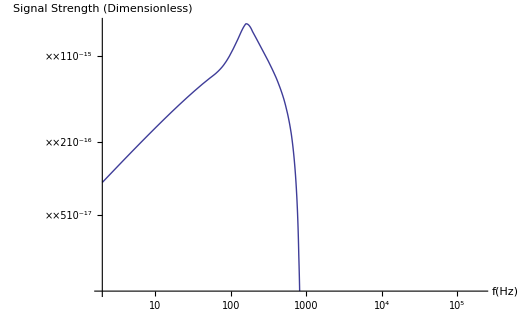

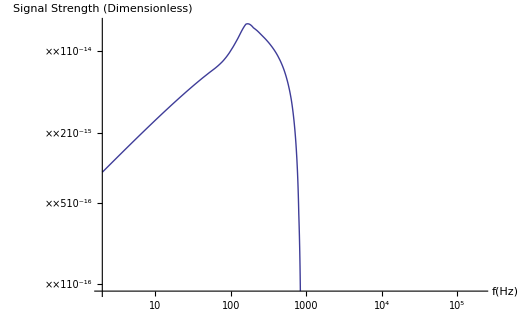

```mathematica
Quiet[LogLogPlot[constant P0[f],{f,10^(.3),10^5.3},AxesLabel->{Style["f(Hz)",Black,Bold,25],Style["Signal Strength\n(Dimensionless)",Black,Bold,25]},
TicksStyle->15,ImageSize->525]]
Quiet[LogLogPlot[constant P1[f] ,{f,10^(.3),10^5.3},AxesLabel->{Style["f(Hz)",Black,Bold,25],Style["Signal Strength\n(Dimensionless)",Black,Bold,25]},
TicksStyle->15,ImageSize->525]]
Quiet[LogLogPlot[constant P2[f],{f,10^(.3),10^5.3},AxesLabel->{Style["f(Hz)",Black,Bold,25],Style["Signal Strength\n(Dimensionless)",Black,Bold,25]},
TicksStyle->15,ImageSize->525]]
```

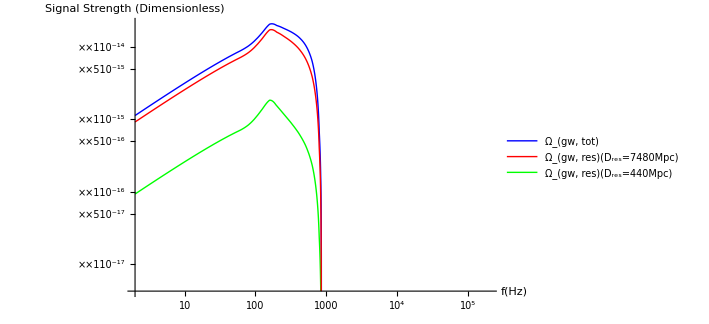

```mathematica
Quiet[LogLogPlot[{constant P0[f],constant P1[f],constant P2[f]},{f,10^(.3),10^5.3},AxesLabel->{Style["f(Hz)",Black,Bold,25],Style["Signal Strength\n(Dimensionless)",Black,Bold,25]},
TicksStyle->20,ImageSize->525,PlotStyle->{Blue,Green,Red},PlotLegends->Placed[LineLegend[{Blue,Red,Green},{Style["Ω_(gw, tot)",Black,Bold,15],Style["Ω_(gw, res)(D_res=7480Mpc)",Black,Bold,15],Style["Ω_(gw, res)(D_res=440Mpc)",Black,Bold,15]}],{0.768,0.50}]]]
```

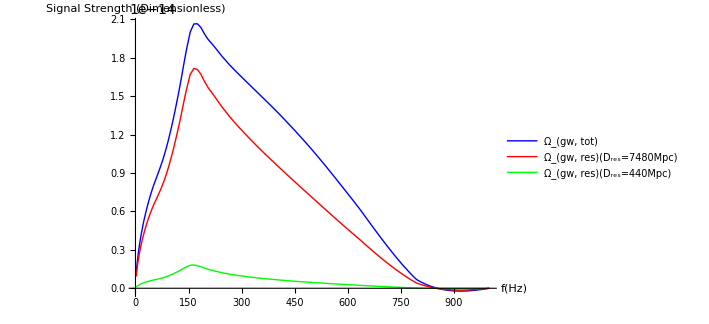

```mathematica
Quiet[Plot[{constant P0[f],constant P1[f],constant P2[f]},{f,10^(.3),10^3},AxesLabel->{Style["f(Hz)",Black,Bold,25],Style["Signal Strength\n(Dimensionless)",Black,Bold,25]},
TicksStyle->20,ImageSize->525,PlotStyle->{Blue,Green,Red},PlotLegends->Placed[LineLegend[{Blue,Red,Green},{Style["Ω_(gw, tot)",Black,Bold,15],Style["Ω_(gw, res)(D_res=7480Mpc)",Black,Bold,15],Style["Ω_(gw, res)(D_res=440Mpc)",Black,Bold,15]}],{0.768,0.50}]]]
```

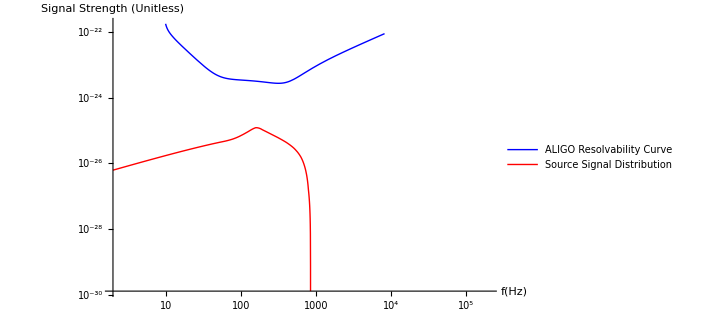

```mathematica
Quiet[LogLogPlot[{If[(DetectorSRDFit["AdvancedLIGO"][f])^(1/2)<1,(DetectorSRDFit["AdvancedLIGO"][f])^(1/2),0],constant P1[f]},{f,10^(.3),10^5.3},AxesLabel->{Style["f(Hz)",Black,Bold,25],Style["Signal Strength\n(Unitless)",Black,Bold,25]},TicksStyle->15,ImageSize->525,PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{Blue,Red},{Style["ALIGO\nResolvability\nCurve",Black,Bold,15],Style["Resolvable Source\nSignal Distribution",Black,Bold,15]}],{0.8,0.54}]]]
```

```mathematica
Quiet[1/NIntegrate[NIntegrate[constant FPDFm[Mc,f],{Mc,10 M0,50 M0}],{f,0,10^3.91}]NIntegrate[If[NIntegrate[0.13864729578627702 constant FPDFm[Mc,f],{Mc,10 M0,50 M0}]>(DetectorSRDFit["AdvancedLIGO"][f])^(1/2),NIntegrate[0.13864729578627702 constant FPDFm[Mc,f],{Mc,10 M0,50 M0}]-(DetectorSRDFit["AdvancedLIGO"][f])^(1/2),0],{f,10,10^3.91}]]
Quiet[1/NIntegrate[NIntegrate[constant FPDFm[Mc,f],{Mc,10 M0,50 M0}],{f,0,10^3.91}]NIntegrate[If[NIntegrate[0.9274959182744076constant FPDFm[Mc,f],{Mc,10 M0,50 M0}]>(DetectorSRDFit["EinsteinTelescope"][f])^(1/2),NIntegrate[0.9274959182744076 constant FPDFm[Mc,f],{Mc,10 M0,50 M0}]-(DetectorSRDFit["EinsteinTelescope"][f])^(1/2),0],{f,10,10^3.91}]]
```

0.

0.877283

```mathematica
Quiet[1/NIntegrate[NIntegrate[constant FPDFm[Mc,f],{Mc,10 M0,50 M0}],{f,0,10^3.91}]NIntegrate[If[NIntegrate[constant FPDFm[Mc,f],{Mc,10 M0,50 M0}]>1/0.13864729578627702(DetectorSRDFit["AdvancedLIGO"][f])^(1/2),NIntegrate[constant FPDFm[Mc,f],{Mc,10 M0,50 M0}]-1/0.13864729578627702(DetectorSRDFit["AdvancedLIGO"][f])^(1/2),0],{f,10,10^3.91}]]
Quiet[1/NIntegrate[NIntegrate[constant FPDFm[Mc,f],{Mc,10 M0,50 M0}],{f,0,10^3.91}]NIntegrate[If[NIntegrate[constant FPDFm[Mc,f],{Mc,10 M0,50 M0}]>1/0.9274959182744076(DetectorSRDFit["EinsteinTelescope"][f])^(1/2),NIntegrate[ constant FPDFm[Mc,f],{Mc,10 M0,50 M0}]-1/0.9274959182744076(DetectorSRDFit["EinsteinTelescope"][f])^(1/2),0],{f,10,10^3.91}]]
```

0.

0.945862